# 4基盤ログの解析:推定ユーザーごとのアクセス推移（ユーザーストーリー）

-Graphics-

グラフ分析部分のみ、save済みグラフを読み込む。

## 準備

```mathematica
start=AbsoluteTime[Date[]]
```

3.910199515789396×10^9

#### 変数

```mathematica
date="20231120"
```

20231120

```mathematica
case={"ci","cs","la","wk"}
```

{ci,cs,la,wk}

```mathematica
base["ci"]="T=ci"
base["cs"]="T=cs"
base["la"]="T=la"
base["wk"]="T=wk"
base["all"]="T=4"
```

T=ci

T=cs

T=la

T=wk

T=4

```mathematica
mountdir="/Volumes/home/NII/togo-log/rcoslogs/"
```

/Volumes/home/NII/togo-log/rcoslogs/

```mathematica
vocdir=mountdir<>"voc"
```

/Volumes/home/NII/togo-log/rcoslogs/voc

#### 解析用データ

```mathematica
fileliststr=Import[mountdir<>"log/D="<>date<>"/"<>"filenames","String"]
```

log-20231120.rcoslog0003.log

```mathematica
filelist=StringSplit[fileliststr]
```

{log-20231120.rcoslog0003.log}

元ログの大きさ （wc）

```mathematica
logwc=Import[mountdir<>"log/D="<>date<>"/logfiles.wc","String"]
```

22645372 320069013 10381193889 log-20231120.rcoslog0003.log

```mathematica
ckanfile=mountdir<>"crid/CIRDEV-1067_crid_list/ckan_product_crid_list.txt"
```

/Volumes/home/NII/togo-log/rcoslogs/crid/CIRDEV-1067_crid_list/ckan_product_crid_list.txt

```mathematica
ckanSt=Import[ckanfile,"String"];
```

```mathematica
(ckanName=StringSplit[ckanSt,"\n"])//Dimensions
```

{92643}

```mathematica
(ckanCridAC=Apply[Association,Map[#->#&,ckanName]])//Dimensions
```

{92643}

#### プログラム

vertexを指定してdirected-edgeを辿る部分グラフ抽出の関数：

```mathematica
directedConnectedGraphComponent[g_,v_]:=Module[{vAll,vOther,addEdge},
vAll=VertexList[g];
vOther=Complement[vAll,{v}];
addEdge=Map[#->v&,vOther];
Subgraph[g,ConnectedComponents[Flatten[{EdgeList[g],addEdge},1],v][[1]]]
]
```

グラフよりinがないノードを検出してそこから(g,v)に対して上記関数をアプライする関数：

```mathematica
vertexInGraph[g_Graph]:=Module[{deg,pos,vname},
deg=VertexInDegree[g];
pos=Position[deg,0]//Flatten//Union;
vname=VertexList[g][[pos]];
Map[directedConnectedGraphComponent[g,#]&,vname]
]
vertexInGraph[g_Integer]:=g
```

story-group-indexを各グラフにdistributeする関数：

```mathematica
distributeIdxGr[idxGr_]:=Module[
{date,idx,gr},
date=idxGr[[1]];
idx=idxGr[[2]];
gr=idxGr[[3]];
Map[{date,idx,#}&,gr]
]
```

stringからfqdnのみ抽出する関数：

```mathematica
fqdnFromPath[s_]:=StringJoin[StringSplit[s,"/"]⟦{1,3}⟧]
```

```mathematica
fqdnFromGraph[g_Graph]:=Union[Sort[Map[fqdnFromPath,VertexList[g]]]]
```

## Analysis

### Get graph

```mathematica
savedir=mountdir<>"log/D="<>date<>"/T=4/_story"
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20231120/T=4/_story

```mathematica
Get[savedir<>"/storyGrIdxFlDs3.save"];
```

### Analysis 1 graph property

基本属性

エッジ:

```mathematica
(eltbl[4]=Table[EdgeList[storyGrIdxFlDs3[4][[i]][[3]]],{i,Length[storyGrIdxFlDs3[4]]}])//Dimensions
```

{186158}

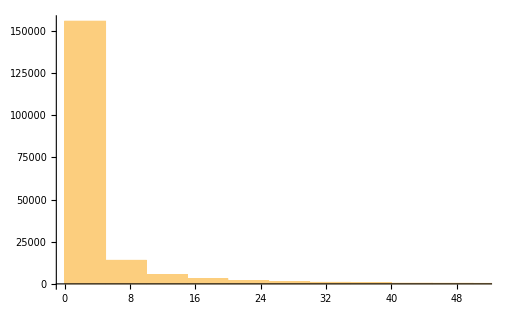

```mathematica
Histogram[Map[Length,eltbl[4]],{5}]
```

ノード:

```mathematica
(vltbl[4]=Table[VertexList[storyGrIdxFlDs3[4][[i]][[3]]],{i,Length[storyGrIdxFlDs3[4]]}])//Dimensions
```

{186158}

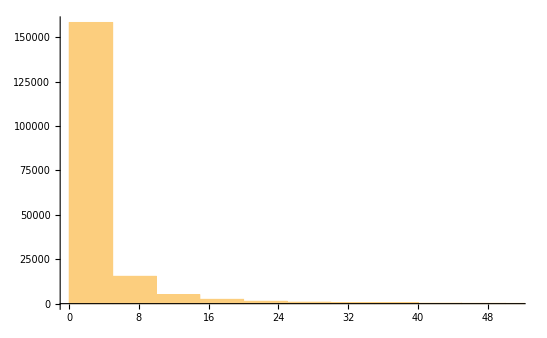

```mathematica
Histogram[Map[Length,vltbl[4]],{5}]
```

アクセス時刻:

```mathematica
(acct[4]=Map[#[[3,1]]&,eltbl[4],{2}])//Dimensions
```

{186158}

滞留時間：

```mathematica
(accspanMin[4]=Map[Max[#]-Min[#]&,acct[4]]/60)//Dimensions
```

{186158}

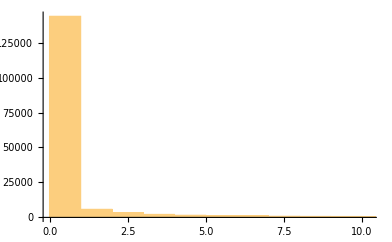

```mathematica
Histogram[accspanMin[4],{1}]
```

スタートノードが最小時刻になっていない。調整が必要か？

E/V ratio:

```mathematica
(ratioEV[4]=Map[Length,eltbl[4]]/Map[Length,vltbl[4]]//N)//Dimensions
```

{186158}

TV ratio :

```mathematica
(ratioTV[4]=acct[4]/Map[Length,vltbl[4]])//Dimensions
```

{186158}

TE ratio:

```mathematica
(ratioTE[4]=acct[4]/Map[Length,eltbl[4]])//Dimensions
```

{186158}

### Analysis 2 base interaction

リクエストパスから基盤名だけをとりだし、基盤連携を見る。

```mathematica
(GrBases[4]=Map[fqdnFromGraph[#[[3]]]&,storyGrIdxFlDs3[4]])//Dimensions
```

Part::partw: Part {1,3} of {cir.nii.ac.jp} does not exist.

StringJoin::string: String expected at position 1 in StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧].

Part::partw: Part {1,3} of {} does not exist.

StringJoin::string: String expected at position 1 in StringJoin[{}⟦{1,3}⟧].

Part::partw: Part {1,3} of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in StringJoin[{}⟦{1,3}⟧].

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

{186158}

NII基盤(4基盤以外も)へのアクセスを見る。

```mathematica
niidnpos=Flatten[Position[Map[StringMatchQ[#,RegularExpression[".*nii.ac.jp.*"]]||StringMatchQ[#,RegularExpression[".*jdcat.jsps.go.jp.*"]]&,Flatten[GrBases[4]]//Union],True]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*nii.ac.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*jdcat.jsps.go.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧],RegularExpression[.*nii.ac.jp.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

{34,40,41,58,61,72,77,103,161,162,166,167,169,181,197,227,228,229,231,232,233,234,235,245,312,332,333,397,401,436,452,460,622,666,730,732,836,882,885,1130,1152,1153,1155,1206,1522,1631}

```mathematica
(Flatten[GrBases[4]]//Union)[[niidnpos]]
```

{http:binder.cs.rcos.nii.ac.jp,http:ci.nii.ac.jp,http:cir.nii.ac.jp,http:grafana.cs.rcos.nii.ac.jp,http:harbor.cs.rcos.nii.ac.jp,http:jdcat.jsps.go.jp,http:jupyter.cs.rcos.nii.ac.jp,http:lms.nii.ac.jp,https:alb-ci-nii-ac-jp-263480797.ap-northeast-1.elb.amazonaws.com,https:alb-ci-nii-ac-jp-263480797.ap-northeast-1.elb.amazonaws.com:443,https:analytics.la.lms.nii.ac.jp,https:analytics.la.test.lms.nii.ac.jp,https:api.ci.nii.ac.jp,https:auth.cir.nii.ac.jp,https:binder.cs.rcos.nii.ac.jp,https:ci.nii.ac.jp,https:ci.nii.ac.jp:443,https:ci-nii-ac-jp.cdn.ampproject.org,https:cir.nii.ac.jp,https:cir-nii-ac-jp.bukkyo.idm.oclc.org,https:cir-nii-ac-jp.nanzan-u.idm.oclc.org,https:cir-nii-ac-jp.swu.idm.oclc.org,https:cir-nii-ac-jp.translate.goog,https:core.orthros.gakunin.nii.ac.jp,https:fukuoka-u.repo.nii.ac.jp,https:ge.nii.ac.jp,https:ge.nii.ac.jp:443,https:idp.nii.ac.jp,https:idp.rdm.nii.ac.jp,https:jdcat.jsps.go.jp,https:jupyter.cs.rcos.nii.ac.jp,https:kaken.nii.ac.jp,https:lms.nii.ac.jp,https:meatwiki.nii.ac.jp,https:niph.repo.nii.ac.jp,https:niu.repo.nii.ac.jp,https:openidp.nii.ac.jp,https:rcos.nii.ac.jp,https:rdm.nii.ac.jp,https:support.nii.ac.jp,https:tohoku.repo.nii.ac.jp,https:tohtech.repo.nii.ac.jp,https:tokoha-u.repo.nii.ac.jp,https:webfront2.nii.ac.jp:443,https:www.nii.ac.jp,https:www.unii.ac.jp}

```mathematica
niigrp=".*\\.nii\\.ac\\.jp.*"
```

.*\.nii\.ac\.jp.*

```mathematica
(GrNiiBases[4]=Map[Cases[#,x_/;StringMatchQ[x,RegularExpression[niigrp]]||StringMatchQ[x,RegularExpression[".*jdcat.jsps.go.jp.*"]]]&,GrBases[4]])//Dimensions
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧],RegularExpression[.*\.nii\.ac\.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧],RegularExpression[.*jdcat.jsps.go.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*\.nii\.ac\.jp.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

{186158}

```mathematica
Map[Length,GrBases[4]]//Tally
```

{{2,164116},{1,22038},{3,4}}

```mathematica
Map[Length,GrNiiBases[4]]//Tally
```

{{1,145613},{2,40545}}

```mathematica
(GrBasesTly[4]=Tally[GrBases[4]])//Dimensions
```

{1794,2}

```mathematica
(GrNiiBasesTly[4]=Tally[GrNiiBases[4]])//Dimensions
```

{45,2}

```mathematica
GrNiiBasesTly[4]//TableForm
```

https:cir.nii.ac.jp | 145398
https:ci.nii.ac.jp
https:cir.nii.ac.jp | 20274
http:ci.nii.ac.jp
https:cir.nii.ac.jp | 19934
https:cir.nii.ac.jp
https:support.nii.ac.jp | 127
http:harbor.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1
https:jdcat.jsps.go.jp | 38
https:cir.nii.ac.jp
https:www.nii.ac.jp | 5
https:ci.nii.ac.jp:443
https:cir.nii.ac.jp | 72
https:jupyter.cs.rcos.nii.ac.jp | 70
https:lms.nii.ac.jp | 107
http:jdcat.jsps.go.jp
https:jdcat.jsps.go.jp | 1
http:cir.nii.ac.jp
https:cir.nii.ac.jp | 46
https:lms.nii.ac.jp
https:www.nii.ac.jp | 1
https:jdcat.jsps.go.jp
https:support.nii.ac.jp | 1
https:cir.nii.ac.jp
https:kaken.nii.ac.jp | 5
https:cir.nii.ac.jp
https:jdcat.jsps.go.jp | 3
https:binder.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 2
https:idp.rdm.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 3
https:cir.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 3
https:cir.nii.ac.jp
https:rcos.nii.ac.jp | 4
https:cir.nii.ac.jp
https:fukuoka-u.repo.nii.ac.jp | 1
https:cir.nii.ac.jp
https:lms.nii.ac.jp | 7
http:grafana.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 10
https:idp.nii.ac.jp
https:lms.nii.ac.jp | 1
https:core.orthros.gakunin.nii.ac.jp
https:lms.nii.ac.jp | 1
https:auth.cir.nii.ac.jp
https:cir.nii.ac.jp | 7
https:cir.nii.ac.jp
https:tohtech.repo.nii.ac.jp | 1
https:jupyter.cs.rcos.nii.ac.jp
https:rdm.nii.ac.jp | 5
https:jupyter.cs.rcos.nii.ac.jp
https:openidp.nii.ac.jp | 8
http:jupyter.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1
https:cir.nii.ac.jp
https:tohoku.repo.nii.ac.jp | 1
https:lms.nii.ac.jp
https:meatwiki.nii.ac.jp | 1
https:cir.nii.ac.jp
https:niph.repo.nii.ac.jp | 1
https:jdcat.jsps.go.jp
https:www.nii.ac.jp | 1
https:analytics.la.lms.nii.ac.jp
https:lms.nii.ac.jp | 6
https:analytics.la.test.lms.nii.ac.jp
https:lms.nii.ac.jp | 1
http:lms.nii.ac.jp
https:lms.nii.ac.jp | 2
http:binder.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1
https:cir.nii.ac.jp
https:ge.nii.ac.jp:443 | 1
https:cir.nii.ac.jp
https:tokoha-u.repo.nii.ac.jp | 1
https:idp.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1
https:api.ci.nii.ac.jp
https:cir.nii.ac.jp | 1
https:cir.nii.ac.jp
https:niu.repo.nii.ac.jp | 1
https:cir.nii.ac.jp
https:ge.nii.ac.jp | 1
https:cir.nii.ac.jp
https:webfront2.nii.ac.jp:443 | 1

グラフが多すぎるので選び方を考え中。

ここから、Idpで認証されたログはIdpがリファラーとして入ってくるが、認証元情報がはいらないため基盤連携のグラフに組み込まれない。
 一方で、Idpを遮蔽して認証元からアクセス先へのエッジは発生する。

### Analysis 3 time series

```mathematica
accessFirst=(Cases[accessTime[4],x_/;x>0]//Min)
```

3.90943×10^9

```mathematica
accessLast=(Cases[accessTime[4],x_/;x>0]//Max)
```

3.90951×10^9

```mathematica
Sort[accessTime["ci"]]//Length
```

2557038

```mathematica
BC600["ci"]=BinCounts[Sort[accessTime["ci"]],{accessFirst,accessLast,60*10}]
```

{15641,15400,14930,17957,17538,16736,16633,18048,17053,17045,19571,14858,17031,14912,12885,14700,14827,19503,17447,16164,14510,11866,10697,10259,12226,11674,12400,13942,11974,14300,11507,12327,11585,12235,13559,11868,9616,12919,14456,12646,14017,14760,13279,14891,11322,12413,14399,14230,12790,14020,12749,11245,11892,14435,14650,17372,16077,16478,15665,15796,14441,15398,16139,15649,17087,16308,16112,19271,19844,19842,19628,17004,15687,14906,14706,15601,17537,16595,17176,18400,17677,19190,21139,23122,20992,23251,21989,21082,24144,20845,20141,21648,24282,23536,24762,22934,20558,22629,23352,23309,24082,23870,23467,23131,20671,19542,21954,18599,17608,20921,22195,18824,20949,20980,19504,21505,19761,20354,21180,20752,20938,20587,19797,21318,20327,17673,18645,19109,19912,20250,20035,21223,21739,21954,20465,20884,20491,21812,20432,22276,22955,22605,22735}

```mathematica
BC600["cs"]=BinCounts[Sort[accessTime["cs"]],{accessFirst,accessLast,60*10}]
```

{1,33,17,26,70,2,12,31,19,3,1,2,5,9,24,2,58,1,2,2,4708,141,6,2,0,1,19,1,59,2,0,0,17,1,0,1,1,2,23,1,58,1,2,0,17,1,2,2,0,0,17,85,60,101,70,16,36,4,1,5,444,0,97,6,428,156,109,121,133,111,226,115,85,44,60,39,98,64,197,652,480,452,934,505,267,243,118,72,236,116,320,176,272,353,128,228,42,7,48,5,91,13,195,196,651,382,273,406,448,18,483,13,66,59,2,3,17,0,2,2,2,2,18,1,60,12,5,0,23,0,6,3,12,3,29,3,62,0,4,1,17,3,0}

```mathematica
BC600["la"]=BinCounts[Sort[accessTime["la"]],{accessFirst,accessLast,60*10}]
```

{2,2,7,0,5,0,74,16,0,0,42,1,1,3,0,3,0,0,1,0,0,45,221,2,57,158,39,1,8,0,2,1,0,8,4,1,0,2,0,2,1,0,26,2,0,12,3,1,0,0,8,8,5,21,0,6,8,3,4,72,36,2,50,63,1,3,127,382,708,733,244,45,37,73,511,288,155,25,39,51,145,67,142,31,3,31,45,82,108,54,2,29,2,1,1,41,118,0,6,1,12,99,130,1,22,6,29,26,2,14,2,7,8,4,2,50,2,6,63,34,8,6,2,3,2,22,4,2,6,7,8,5,2,5,4,31,101,108,4,10,2,3,16}

```mathematica
BC600["wk"]=BinCounts[Sort[accessTime["wk"]],{accessFirst,accessLast,60*10}]
```

{38,47,74,46,11,2,13,18,17,0,10,4,27,20,28,26,23,14,27,52,43,45,48,40,36,38,36,36,38,58,23,11,31,70,51,53,28,45,63,42,40,13,47,43,48,42,44,12,42,40,54,64,19,7,53,54,43,70,74,30,62,34,28,22,34,61,50,39,62,43,71,41,39,38,53,38,40,40,34,36,45,69,77,56,48,43,54,43,71,58,67,115,231,82,42,23,33,44,45,42,55,25,38,50,55,55,57,12,66,53,62,57,126,207,65,34,58,47,56,39,25,42,75,68,47,35,45,49,37,36,51,21,52,51,1,45,50,29,12,29,35,48,36}

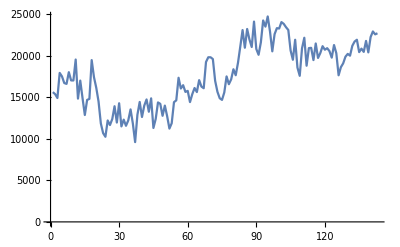

```mathematica
ListPlot[BC600["ci"],PlotRange->Full,Joined->True]
```

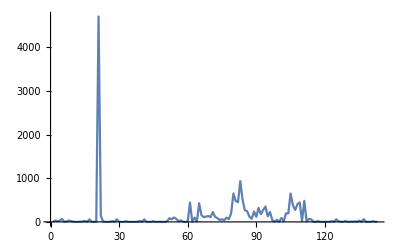

```mathematica
ListPlot[BC600["cs"],PlotRange->Full,Joined->True]
```

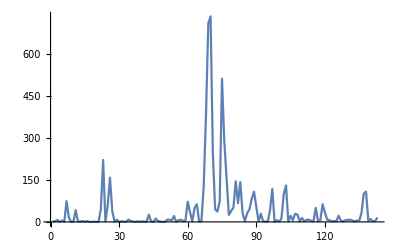

```mathematica
ListPlot[BC600["la"],PlotRange->Full,Joined->True]
```

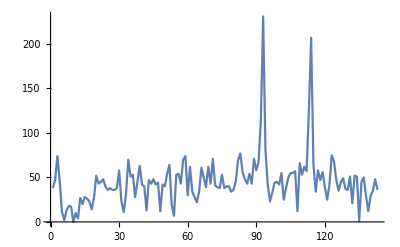

```mathematica
ListPlot[BC600["wk"],PlotRange->Full,Joined->True]
```

### Analysis 4 CKAN impact

ckanCRIDを含むグラフを抽出する。

すでに構成したハッシュとグラフのプロパティを当てる関数。ひとつでもあたればTrueを返す。
 ハッシュはログ中の位置を記述しており、リクエストパス・リファラーを分けたもの、Unionしたもの。

滞留時間をグラフから得る関数：

```mathematica
stayTime[g_Graph]:=Module[{elist,tlist},
elist=EdgeList[g];
tlist=Map[#[[3,1]]&,elist];
Max[tlist]-Min[tlist]
]
```

ckanCRIDを含むログの行とグラフのエッジにあるログの行を当てる関数 （T/F）:

```mathematica
logGraphQ[gr_Graph,asc_Association]:=Module[{elist,logposlist,res},
elist=EdgeList[gr];
logposlist=Map[#[[3,2]]&,elist];
res=Map[asc[#]&,logposlist];
Position[res,_Integer,{1}]/.{{}->False,{__}->True}
]
```

ckanCRIDをリクエストに含むノードをハイライトする関数：

```mathematica
toCRID[s_String/;StringMatchQ[s,RegularExpression["https://cir.nii.ac.jp/crid/.*"]]]:=StringTake[StringSplit[s,"/"][[5]],19]
```

```mathematica
ckanVertexHighlihgt[g_Graph,asc_Association]:=Module[{vlist,pos,targetv,op},
vlist=VertexList[g];
pos=Flatten[Position[Map[ckanCridPRACQ[toCRID[#]]&,VertexList[g]],True]];
targetv=vlist[[pos]];
op=VertexStyle->Map[#->Red&,targetv];
Graph[g,op]
]
```

CKAN - CRIDを含むグラフの抽出

```mathematica
(ckanGrP[4]=Map[If[logGraphQ[#[[3]],ckanCridPLogPosAC[4]],#,Null]&,storyGrIdxFlDs3[4]])//Dimensions
```

{186158}

```mathematica
(ckanGrR[4]=Map[If[logGraphQ[#[[3]],ckanCridRLogPosAC[4]],#,Null]&,storyGrIdxFlDs3[4]])//Dimensions
```

{186158}

```mathematica
(ckanGrPR[4]=Map[If[logGraphQ[#[[3]],ckanCridPRLogPosAC[4]],#,Null]&,storyGrIdxFlDs3[4]])//Dimensions
```

{186158}

```mathematica
(ckanGrPsel[4]=Cases[ckanGrP[4],{__},{1}])//Dimensions
```

{99,3}

```mathematica
ckanGrPselVL[4]=Map[VertexList[#[[3]]]&,ckanGrPsel[4]];
```

```mathematica
ckanGrPselEL[4]=Map[EdgeList[#[[3]]]&,ckanGrPsel[4]];
```

```mathematica
(ckanGrRsel[4]=Cases[ckanGrR[4],{__},{1}])//Dimensions
```

{17,3}

```mathematica
ckanGrRselVL[4]=Map[VertexList[#[[3]]]&,ckanGrRsel[4]];
```

```mathematica
ckanGrRselEL[4]=Map[EdgeList[#[[3]]]&,ckanGrRsel[4]];
```

```mathematica
(ckanGrPRsel[4]=Cases[ckanGrPR[4],{__},{1}])//Dimensions
```

{101,3}

```mathematica
ckanGrPRselVL[4]=Map[VertexList[#[[3]]]&,ckanGrPRsel[4]];
```

```mathematica
ckanGrPRselEL[4]=Map[EdgeList[#[[3]]]&,ckanGrPRsel[4]];
```

```mathematica
(ckanGrPRselHL[4]=Map[{#[[1]],#[[2]],ckanVertexHighlihgt[#[[3]],ckanCridPRACQ]}&,ckanGrPRsel[4]])//Dimensions
```

{101,3}

```mathematica
ckanGrPRVcount[4]=Map[VertexCount[#[[3]]]&,ckanGrPRselHL[4]]
```

{2,8,14,2,5,14,34,2,2,2,2,2,93,92,93,37,21,43,105,14,9,2,13,26,10,20,2,19,35,269,265,265,41,46,67,6,31,18,18,25,11,12,12,6,8,13,26,14,14,17,45,2,27,41,45,7,22,12,14,16,24,8,18,68,72,69,65,423,423,462,423,423,426,423,11,17,94,99,95,62,14,2,23,4,2,25,6,29,16,23,36,36,36,9,7,18,11,3,6,1099,17}

```mathematica
accTimeList[g_Graph]:=Module[{elist,tlist},
elist=EdgeList[g];
tlist=Sort[Map[#[[3,1]]&,elist],#1>#2&]
]
```

```mathematica
timeSpan[tlist_]:=Map[(#[[1]]-#[[2]])&,Partition[tlist,2,1]]
```

```mathematica
ckanGrPRstayTime[4]=Map[stayTime[#[[3]]]&,ckanGrPRselHL[4]]
```

{0.,181.,236.,0.,62.,10090.,29306.,0.,0.,0.,0.,0.,19258.,19246.,19246.,2084.,16014.,4963.,35597.,1652.,779.,0.,1471.,1522.,7197.,3292.,0.,3870.,3960.,12997.,3326.,3326.,17575.,29621.,30254.,38.,28696.,8609.,8648.,5124.,2778.,698.,145.,154.,218.,13946.,14936.,13946.,746.,547.,80409.,0.,27159.,14603.,5688.,103.,15398.,1778.,2091.,11978.,13402.,17069.,12300.,18443.,28412.,22531.,18443.,33342.,33342.,41975.,33342.,34501.,33342.,33342.,1610.,13257.,26838.,26826.,26826.,4057.,1811.,0.,6275.,22.,0.,12197.,10232.,3259.,7351.,736.,1259.,1222.,1222.,196.,177.,620.,1537.,5.,25958.,86309.,1379.}

### Analysis 5 CKAN graph reform

program :

可能な全Vertexにアクセス時間リストを付与：

```mathematica
gatherDistributeUniq[l_]:=Module[{first,target},
first=l[[1,1]];
target=Map[#[[2]]&,l];
{first,target}
]
```

```mathematica
gatherDistributeUniqRl[l_]:=Module[{first,target},
first=l[[1,1]];
target=Map[#[[2]]&,l];
first->{first,target}
]
```

```mathematica
addVertexAccTime[g_]:=Module[{gatherTimeV,gatherTimeVRl},
gatherTimeV=Gather[Map[{#[[2]],#[[3,1]]}&,EdgeList[g]],#1[[1]]==#2[[1]]&];
gatherTimeVRl=Map[gatherDistributeUniqRl,gatherTimeV];
VertexReplace[g,gatherTimeVRl]
]
```

```mathematica
guessVertexCoorGr[g_,timeshift_]:=Module[{allAccTime,baseTime,repPos,target,repRl},
allAccTime=Cases[Flatten[Map[#[[2]]&,g//VertexList]],_Real];
baseTime=Min[allAccTime]+timeshift;
repPos=Flatten[Position[Map[Head,VertexList[g]],String]];
target=Map[VertexList[g][[#]]&,repPos];
repRl=Map[#->{#,{baseTime}}&,target];
VertexReplace[g,repRl]
]
```

```mathematica
accTimeMinGr[g_]:=Min[Cases[Flatten[Map[#[[2]]&,g//VertexList]],_Real]]
```

```mathematica
reformCoorGr[g_,baseTime_,f_]:=f[Map[{Max[#[[2]]],Min[#[[2]]]}&,VertexList[g]]-baseTime]
```

```mathematica
timeLineGr[g_,timeshift_,f_]:=Module[{gnew,btime,coornew},
gnew=guessVertexCoorGr[g,timeshift];
btime=accTimeMinGr[gnew];
coornew=reformCoorGr[gnew,btime,Sqrt];
Graph[gnew,VertexSize->Automatic,VertexCoordinates->coornew]
]
```

```mathematica
(ckanGrPRselHLAT[4]=Map[{#[[1]],#[[2]],addVertexAccTime[#[[3]]]}&,ckanGrPRselHL[4]])//Dimensions
```

{101,3}

ロググループ：

```mathematica
loggroupCKAN=Map[#[[2]]&,ckanGrPRselHLAT[4]]
```

{{1573,1},{7088,1},{8561,1},{11060,1},{15038,1},{19369,1},{19523,1},{21370,1},{21376,1},{21473,1},{21689,1},{28729,1},{28985,1},{28985,1},{28985,1},{29113,1},{29234,1},{29989,1},{33554,1},{36594,1},{37594,1},{42418,1},{43890,1},{48565,1},{49170,1},{49733,1},{51268,1},{51701,1},{56865,1},{59808,1},{59808,1},{59808,1},{62885,1},{63160,1},{63160,1},{64191,1},{64540,1},{64540,1},{64540,1},{72164,1},{72525,1},{74616,1},{75978,1},{81946,1},{85006,1},{85040,1},{85040,1},{85040,1},{94427,1},{99062,1},{99527,1},{101752,1},{101976,1},{102058,1},{102058,1},{103687,1},{104234,1},{104542,1},{104542,1},{104543,1},{104543,1},{104547,1},{104723,1},{105495,1},{105495,1},{105495,1},{105495,1},{105656,1},{105656,1},{105656,1},{105656,1},{105656,1},{105656,1},{105656,1},{105818,1},{105995,1},{106034,1},{106034,1},{106034,1},{107495,1},{110150,1},{110827,1},{111828,1},{112121,1},{113304,1},{114843,1},{118439,1},{119104,1},{119131,1},{120483,1},{121377,1},{121377,1},{121377,1},{124284,1},{126924,1},{140067,1},{142820,1},{147019,1},{155586,1},{159917,1},{163950,1}}

ノードの数え上げ：

```mathematica
vcCKAN=Map[VertexCount[#[[3]]]&,ckanGrPRselHLAT[4]]
```

{2,8,14,2,5,14,34,2,2,2,2,2,93,92,93,37,21,43,105,14,9,2,13,26,10,20,2,19,35,269,265,265,41,46,67,6,31,18,18,25,11,12,12,6,8,13,26,14,14,17,45,2,27,41,45,7,22,12,14,16,24,8,18,68,72,69,65,423,423,462,423,423,426,423,11,17,94,99,95,62,14,2,23,4,2,25,6,29,16,23,36,36,36,9,7,18,11,3,6,1099,17}

エッジの数え上げ：

```mathematica
ecCKAN=Map[EdgeCount[#[[3]]]&,ckanGrPRselHLAT[4]]
```

{1,14,28,1,5,15,59,1,1,1,1,1,153,140,150,55,42,63,148,15,12,1,17,52,13,42,1,32,75,667,512,513,56,83,111,5,43,22,23,29,13,14,19,6,8,15,34,16,17,23,68,1,37,76,81,12,30,13,16,25,40,9,22,92,108,98,94,650,652,743,652,656,657,652,26,45,265,269,267,100,20,1,27,4,1,64,5,87,18,35,50,48,49,14,7,37,15,2,5,1373,22}

アクセス時刻：

```mathematica
(accCKAN=Map[Map[#[[3,1]]&,EdgeList[#[[3]]]]&,ckanGrPRselHLAT[4]])//Dimensions
```

{101}

最大滞在時間：

```mathematica
maxTimeSpan[l_]:=Max[Map[#[[1]]-#[[2]]&,Partition[Sort[l,#1>#2&],2,1]]]
```

```mathematica
(maxtimespanCKAN=Map[maxTimeSpan,accCKAN]/.{-Infinity->0})/60
```

{0,0.716667,1.03333,0,0.433333,86.7333,464.733,0,0,0,0,0,64.7833,72.8333,72.8333,11.2833,243.067,67.05,351.3,7.96667,7.68333,0,15.95,16.8,73.05,19.5833,0,21.1167,37.7833,107.017,7.48333,7.48333,151.6,273.583,344.167,0.3,171.733,128.767,128.767,37.0667,37.55,8.03333,0.416667,2.05,1.78333,228.283,175.817,227.85,4.78333,6.01667,1107.65,0,160.133,139.1,54.85,0.65,157.65,26.65,26.4667,99.0333,98.8167,280.433,192.583,88.9167,107.2,168.25,168.25,67.6,67.6,94.25,67.6,67.6,67.6,67.6,11.4667,100.233,118.8,118.8,118.717,10.8667,6.05,0,89.9167,0.2,0,120.667,134.833,7.85,61.5333,2.63333,4.81667,4.81667,4.81667,2.15,1.06667,2.08333,15.2667,0.0833333,240.6,26.95,13.7667}

滞留時間：

```mathematica
staytimeCKAN=Map[Max[#]-Min[#]&,accCKAN]
```

{0.,181.,236.,0.,62.,10090.,29306.,0.,0.,0.,0.,0.,19258.,19246.,19246.,2084.,16014.,4963.,35597.,1652.,779.,0.,1471.,1522.,7197.,3292.,0.,3870.,3960.,12997.,3326.,3326.,17575.,29621.,30254.,38.,28696.,8609.,8648.,5124.,2778.,698.,145.,154.,218.,13946.,14936.,13946.,746.,547.,80409.,0.,27159.,14603.,5688.,103.,15398.,1778.,2091.,11978.,13402.,17069.,12300.,18443.,28412.,22531.,18443.,33342.,33342.,41975.,33342.,34501.,33342.,33342.,1610.,13257.,26838.,26826.,26826.,4057.,1811.,0.,6275.,22.,0.,12197.,10232.,3259.,7351.,736.,1259.,1222.,1222.,196.,177.,620.,1537.,5.,25958.,86309.,1379.}

```mathematica
staytimeCKAN/60
```

{0.,3.01667,3.93333,0.,1.03333,168.167,488.433,0.,0.,0.,0.,0.,320.967,320.767,320.767,34.7333,266.9,82.7167,593.283,27.5333,12.9833,0.,24.5167,25.3667,119.95,54.8667,0.,64.5,66.,216.617,55.4333,55.4333,292.917,493.683,504.233,0.633333,478.267,143.483,144.133,85.4,46.3,11.6333,2.41667,2.56667,3.63333,232.433,248.933,232.433,12.4333,9.11667,1340.15,0.,452.65,243.383,94.8,1.71667,256.633,29.6333,34.85,199.633,223.367,284.483,205.,307.383,473.533,375.517,307.383,555.7,555.7,699.583,555.7,575.017,555.7,555.7,26.8333,220.95,447.3,447.1,447.1,67.6167,30.1833,0.,104.583,0.366667,0.,203.283,170.533,54.3167,122.517,12.2667,20.9833,20.3667,20.3667,3.26667,2.95,10.3333,25.6167,0.0833333,432.633,1438.48,22.9833}

```mathematica
f[x_]=Log[x+1]
```

Log[1+x]

```mathematica
(ckanGrPRselHLTL[4]=Map[timeLineGr[#[[3]],-60,f]&,ckanGrPRselHLAT[4]])//Dimensions
```

Part::partd: Part specification https://www.google.com/⟦2⟧ is longer than depth of object.

Part::partd: Part specification https://www.google.com/url?q=https://cir.nii.ac.jp/&sa=U&sqi=2&ved=2ahUKEwihwqOM0dGCAxVGNN4KHW73BGMQFnoECAcQAQ&usg=AOvVaw1TP0cPw4owrZdTH0aWcRIf⟦2⟧ is longer than depth of object.

Part::partd: Part specification https://www.google.com/url?q=https://cir.nii.ac.jp/&sa=U&sqi=2&ved=2ahUKEwiaq_TUkNKCAxUPsFYBHRnID74QFnoECAUQAQ&usg=AOvVaw3bwiI2wZC5Md_ZZTpkmgcf⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{101}

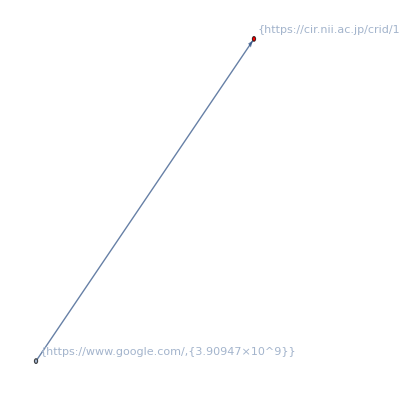

```mathematica
ckanGrPRselHLTL[4][[1]]
```

### Analysis 6 CKAN voc-graph

vocRlの読み込み：

```mathematica
vocRlFiles=FileNames[vocdir<>"/*.wl"]
```

{/Volumes/home/NII/togo-log/rcoslogs/voc/voc_path_action_ci_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_path_action_cs_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_path_action_la_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_path_action_wk_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_ref_action_ci_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_ref_action_cs_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_ref_action_la_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_ref_action_wk_rl.wl}

```mathematica
vocRlList=Map[Get,vocRlFiles];
```

```mathematica
(vocRl["all:path"]=Apply[Join,vocRlList])//Dimensions
```

{113}

```mathematica
vocRl["all:path"][[1]]
```

x_/;StringMatchQ[x,RegularExpression[https://cir.nii.ac.jp/]]→voc[ci:top]

===== /プログラム検討 =====

====== /引数 ======

```mathematica
gr=ckanGrPRselHLTL[4][[1]]
```

-Graphics-

```mathematica
rl=vocRl["all:path"];
```

====== 引数/ ======

====== /内部変数 ======

```mathematica
vl=VertexList[gr]
```

{{https://www.google.com/,{3.90947×10^9}},{https://cir.nii.ac.jp/crid/1690013498967485824,{3.90947×10^9}}}

```mathematica
vname=Map[#[[1]]&,vl]
```

{https://www.google.com/,https://cir.nii.ac.jp/crid/1690013498967485824}

```mathematica
vrename=(vname/.rl)
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/ja]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/\?.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

{https://www.google.com/,voc[ci:detail]}

```mathematica
vrenameRl=Map[Apply[Rule,#]&,Transpose[{vl,vrename}]]
```

{{https://www.google.com/,{3.90947×10^9}}→https://www.google.com/,{https://cir.nii.ac.jp/crid/1690013498967485824,{3.90947×10^9}}→voc[ci:detail]}

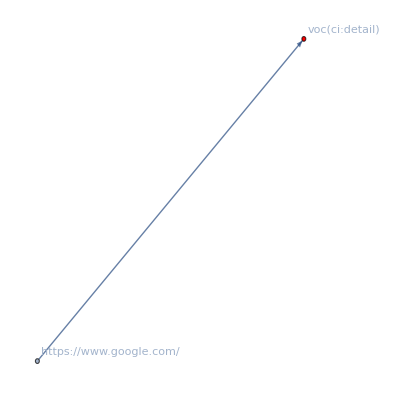

```mathematica
Graph[gr,VertexLabels->vrenameRl]
```

====== 内部変数/ ======

===== プログラム検討/ =====

```mathematica
toVocGraph[gr_,rl_]:=Module[{vl,vname,vrename,vrenameRl},
Print["it may cause StringMatchQ warn."];
vl=VertexList[gr];
vname=Map[#[[1]]&,vl];
vrename=(vname/.rl);
vrenameRl=Map[Apply[Rule,#]&,Transpose[{vl,vrename}]];
Graph[gr,VertexLabels->vrenameRl]
]
```

```mathematica
toVocGraph[ckanGrPRselHLTL[4][[1]],vocRl["all:path"]]
```

it may cause StringMatchQ warn.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/ja]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/\?.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

-Graphics-

it may cause StringMatchQ warn.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/ja]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/\?.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

it may cause StringMatchQ warn.

it may cause StringMatchQ warn.

it may cause StringMatchQ warn.

«97 more identical outputs»

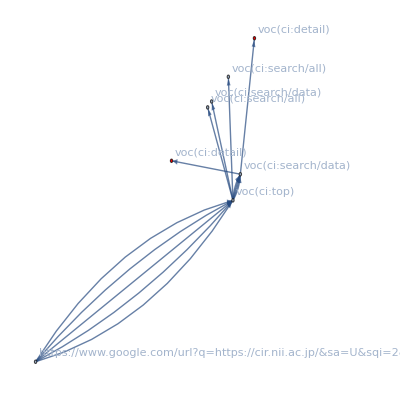
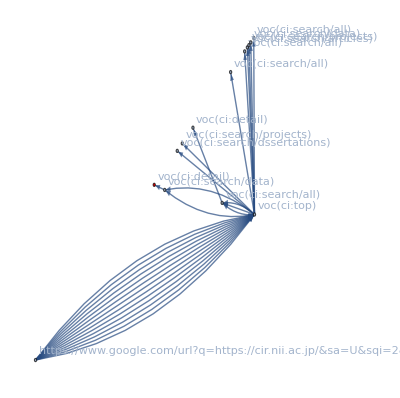
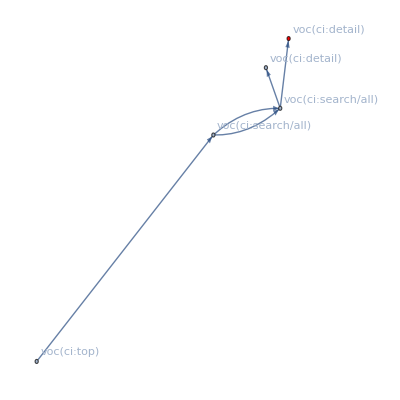
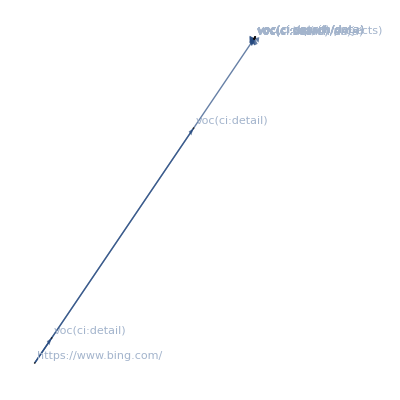
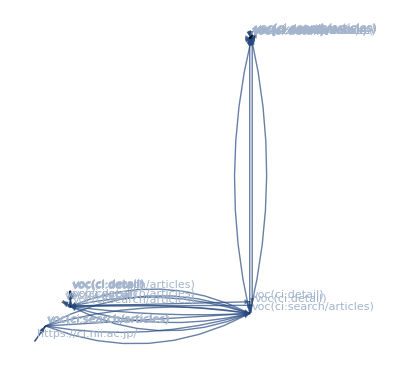
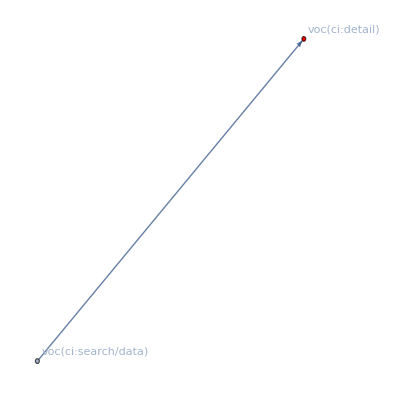
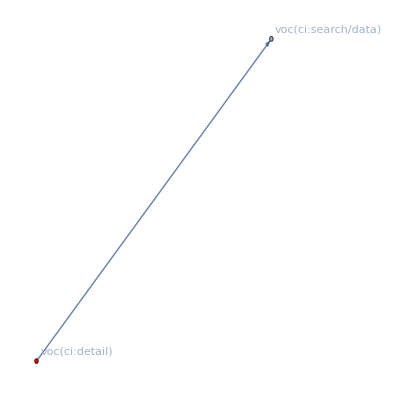
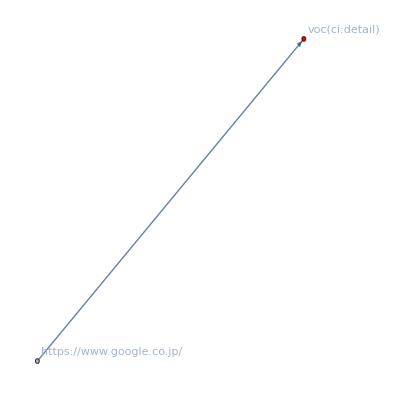
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
Map[toVocGraph[#,vocRl["all:path"]]&,ckanGrPRselHLTL[4]]//TableForm
```

### Report:CKAN impact

```mathematica
(logTotal={{"- ログ件数 -","述べログ件数"},{"全件数",ToExpression[StringSplit[logwc][[1]]]},{"ユーザーアクセス件数",idxLogLen[4]}})//TableForm
```

- ログ件数 - | 述べログ件数
全件数 | 22645372
ユーザーアクセス件数 | 2587373

```mathematica
(ckanLogTotal={{"- CKAN-cridを含むログ件数 -","述べログ件数","cridのユニーク件数"},
{"リクエストにCKAN-crid含む",ckanCridPLogPos[4]//Length,Union[ckanCridPlist]//Length},
{"リファラーにCKAN-crid含む",ckanCridRLogPos[4]//Length,Union[ckanCridRlist]//Length},
{"いずれか含む",ckanCridPRLogPos[4]//Length,ckanCridPRU//Length}
})//TableForm
```

- CKAN-cridを含むログ件数 - | 述べログ件数 | cridのユニーク件数
リクエストにCKAN-crid含む | 188 | 159
リファラーにCKAN-crid含む | 25 | 14
いずれか含む | 213 | 159

```mathematica
(ckanChainTotal={{"- アクション連鎖数 -","件数"},
{"全件数",storyGrIdxFlDs3[4]//Length},
{"ノードにCKAN-crid含む",ckanGrPRselHL[4]//Length}
})//TableForm
```

- アクション連鎖数 - | 件数
全件数 | 186158
ノードにCKAN-crid含む | 101

```mathematica
(ckanGraphSummary=Prepend[Transpose[{Table[i,{i,Length[loggroupCKAN]}],loggroupCKAN,vcCKAN,ecCKAN,maxtimespanCKAN/60,staytimeCKAN/60}],{"アクセスグラフ通し番号","ロググループ","ノード数","エッジ数","最大滞在時間(分)","滞留時間(分)"}])//TableForm
```

アクセスグラフ通し番号 | ロググループ | ノード数 | エッジ数 | 最大滞在時間(分) | 滞留時間(分)
1 | 1573
1 | 2 | 1 | 0 | 0.
2 | 7088
1 | 8 | 14 | 0.716667 | 3.01667
3 | 8561
1 | 14 | 28 | 1.03333 | 3.93333
4 | 11060
1 | 2 | 1 | 0 | 0.
5 | 15038
1 | 5 | 5 | 0.433333 | 1.03333
6 | 19369
1 | 14 | 15 | 86.7333 | 168.167
7 | 19523
1 | 34 | 59 | 464.733 | 488.433
8 | 21370
1 | 2 | 1 | 0 | 0.
9 | 21376
1 | 2 | 1 | 0 | 0.
10 | 21473
1 | 2 | 1 | 0 | 0.
11 | 21689
1 | 2 | 1 | 0 | 0.
12 | 28729
1 | 2 | 1 | 0 | 0.
13 | 28985
1 | 93 | 153 | 64.7833 | 320.967
14 | 28985
1 | 92 | 140 | 72.8333 | 320.767
15 | 28985
1 | 93 | 150 | 72.8333 | 320.767
16 | 29113
1 | 37 | 55 | 11.2833 | 34.7333
17 | 29234
1 | 21 | 42 | 243.067 | 266.9
18 | 29989
1 | 43 | 63 | 67.05 | 82.7167
19 | 33554
1 | 105 | 148 | 351.3 | 593.283
20 | 36594
1 | 14 | 15 | 7.96667 | 27.5333
21 | 37594
1 | 9 | 12 | 7.68333 | 12.9833
22 | 42418
1 | 2 | 1 | 0 | 0.
23 | 43890
1 | 13 | 17 | 15.95 | 24.5167
24 | 48565
1 | 26 | 52 | 16.8 | 25.3667
25 | 49170
1 | 10 | 13 | 73.05 | 119.95
26 | 49733
1 | 20 | 42 | 19.5833 | 54.8667
27 | 51268
1 | 2 | 1 | 0 | 0.
28 | 51701
1 | 19 | 32 | 21.1167 | 64.5
29 | 56865
1 | 35 | 75 | 37.7833 | 66.
30 | 59808
1 | 269 | 667 | 107.017 | 216.617
31 | 59808
1 | 265 | 512 | 7.48333 | 55.4333
32 | 59808
1 | 265 | 513 | 7.48333 | 55.4333
33 | 62885
1 | 41 | 56 | 151.6 | 292.917
34 | 63160
1 | 46 | 83 | 273.583 | 493.683
35 | 63160
1 | 67 | 111 | 344.167 | 504.233
36 | 64191
1 | 6 | 5 | 0.3 | 0.633333
37 | 64540
1 | 31 | 43 | 171.733 | 478.267
38 | 64540
1 | 18 | 22 | 128.767 | 143.483
39 | 64540
1 | 18 | 23 | 128.767 | 144.133
40 | 72164
1 | 25 | 29 | 37.0667 | 85.4
41 | 72525
1 | 11 | 13 | 37.55 | 46.3
42 | 74616
1 | 12 | 14 | 8.03333 | 11.6333
43 | 75978
1 | 12 | 19 | 0.416667 | 2.41667
44 | 81946
1 | 6 | 6 | 2.05 | 2.56667
45 | 85006
1 | 8 | 8 | 1.78333 | 3.63333
46 | 85040
1 | 13 | 15 | 228.283 | 232.433
47 | 85040
1 | 26 | 34 | 175.817 | 248.933
48 | 85040
1 | 14 | 16 | 227.85 | 232.433
49 | 94427
1 | 14 | 17 | 4.78333 | 12.4333
50 | 99062
1 | 17 | 23 | 6.01667 | 9.11667
51 | 99527
1 | 45 | 68 | 1107.65 | 1340.15
52 | 101752
1 | 2 | 1 | 0 | 0.
53 | 101976
1 | 27 | 37 | 160.133 | 452.65
54 | 102058
1 | 41 | 76 | 139.1 | 243.383
55 | 102058
1 | 45 | 81 | 54.85 | 94.8
56 | 103687
1 | 7 | 12 | 0.65 | 1.71667
57 | 104234
1 | 22 | 30 | 157.65 | 256.633
58 | 104542
1 | 12 | 13 | 26.65 | 29.6333
59 | 104542
1 | 14 | 16 | 26.4667 | 34.85
60 | 104543
1 | 16 | 25 | 99.0333 | 199.633
61 | 104543
1 | 24 | 40 | 98.8167 | 223.367
62 | 104547
1 | 8 | 9 | 280.433 | 284.483
63 | 104723
1 | 18 | 22 | 192.583 | 205.
64 | 105495
1 | 68 | 92 | 88.9167 | 307.383
65 | 105495
1 | 72 | 108 | 107.2 | 473.533
66 | 105495
1 | 69 | 98 | 168.25 | 375.517
67 | 105495
1 | 65 | 94 | 168.25 | 307.383
68 | 105656
1 | 423 | 650 | 67.6 | 555.7
69 | 105656
1 | 423 | 652 | 67.6 | 555.7
70 | 105656
1 | 462 | 743 | 94.25 | 699.583
71 | 105656
1 | 423 | 652 | 67.6 | 555.7
72 | 105656
1 | 423 | 656 | 67.6 | 575.017
73 | 105656
1 | 426 | 657 | 67.6 | 555.7
74 | 105656
1 | 423 | 652 | 67.6 | 555.7
75 | 105818
1 | 11 | 26 | 11.4667 | 26.8333
76 | 105995
1 | 17 | 45 | 100.233 | 220.95
77 | 106034
1 | 94 | 265 | 118.8 | 447.3
78 | 106034
1 | 99 | 269 | 118.8 | 447.1
79 | 106034
1 | 95 | 267 | 118.717 | 447.1
80 | 107495
1 | 62 | 100 | 10.8667 | 67.6167
81 | 110150
1 | 14 | 20 | 6.05 | 30.1833
82 | 110827
1 | 2 | 1 | 0 | 0.
83 | 111828
1 | 23 | 27 | 89.9167 | 104.583
84 | 112121
1 | 4 | 4 | 0.2 | 0.366667
85 | 113304
1 | 2 | 1 | 0 | 0.
86 | 114843
1 | 25 | 64 | 120.667 | 203.283
87 | 118439
1 | 6 | 5 | 134.833 | 170.533
88 | 119104
1 | 29 | 87 | 7.85 | 54.3167
89 | 119131
1 | 16 | 18 | 61.5333 | 122.517
90 | 120483
1 | 23 | 35 | 2.63333 | 12.2667
91 | 121377
1 | 36 | 50 | 4.81667 | 20.9833
92 | 121377
1 | 36 | 48 | 4.81667 | 20.3667
93 | 121377
1 | 36 | 49 | 4.81667 | 20.3667
94 | 124284
1 | 9 | 14 | 2.15 | 3.26667
95 | 126924
1 | 7 | 7 | 1.06667 | 2.95
96 | 140067
1 | 18 | 37 | 2.08333 | 10.3333
97 | 142820
1 | 11 | 15 | 15.2667 | 25.6167
98 | 147019
1 | 3 | 2 | 0.0833333 | 0.0833333
99 | 155586
1 | 6 | 5 | 240.6 | 432.633
100 | 159917
1 | 1099 | 1373 | 26.95 | 1438.48
101 | 163950
1 | 17 | 22 | 13.7667 | 22.9833

### Export:CKAN impact

エッジリスト：

```mathematica
(ckanEL=Map[MapApply[List,EdgeList[#]]&,ckanGrPRselHLTL[4]])//Dimensions
```

{101}

```mathematica
ckanELexp=Map[{#[[1,1]],#[[2,1]]}&,ckanEL,{2}];
```

```mathematica
expdir=mountdir<>"log/D="<>date<>"/T=4/_story"
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20231120/T=4/_story

```mathematica
SetDirectory[expdir]
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20231120/T=4/_story

```mathematica
Export["ckanedgelist.json",ckanELexp]
```

ckanedgelist.json

ログ件数、ckanグラフまとめ：

```mathematica
Export["graphProperty.xlsx",{logTotal,ckanLogTotal,ckanChainTotal,ckanGraphSummary}]
```

graphProperty.xlsx

## 終端処理

```mathematica
end=AbsoluteTime[Date[]]
```

3.910199586274587×10^9

```mathematica
end-start
```

70.485191